### Supplementary code for simulations of D. suzukii population dynamics in “Large-scale open field trials in California and Oregon to evaluate the potential use of a new behavioral control system for Drosophila suzukii Matsumura (Diptera: Drosophilidae)” by Tait et al. 2022 Contact for code: ferdinand.pfab@gmail.com This file fits the model functions to data from the literature.

```mathematica
(*Data from Tochen et al '14, table 2: blueberries*)
(*experimental temperatures in C*)
tochentemps={10,14,18,22,26,28};
(*average time from egg to pupa at different temperatures (sum of egg and larva duration)*)
ttimeseggtopupa={43.6,16.2,11.7,8.2,6.6,5.9};
(*proportion of this time spend in egg stage, from Emiljanovic et al 2014*)
propeggtoeggpluslarva=.2;
(*average time in egg stage*)
ttimeseggtolarva=propeggtoeggpluslarva ttimeseggtopupa;
(*average time in larva stage*)
ttimeslarvatopupa=(1-propeggtoeggpluslarva) ttimeseggtopupa;
(*average time in pupa stage*)
ttimespupatoadult={33.8,12.7,8.5,6.0,4.6,4.2};
(*average time of all juvenile stages together, for calculating mortality rates below*)
ttimeseggtoadult={77.4,28.3,20.1,14,10.9,10.1};
(*average life time of adult*)
ttimesadulttomortality={24.4,16.6,17,11.7,12.1,12};
(*how many individuals survive all juvenile stages, relative to the 100 individuals the trials were started with*)
eggtopupasurvival=({5,26,22,41,48,19}+{5,16,16,39,42,20})/100.;
(*temperatures for fecundity trials (excluding first temperature of other trials)*)
fecunditytemp=tochentemps[[2;;-1]];
(*lifetime fecundities of females*)
fecundityvals={6.6,17,19.8,12.1,7.3};
(*fecundity per day, using average adult life length at the corresponding temperatures*)
fecundityvalsperday=Table[fecundityvals[[i]]/ttimesadulttomortality[[i+1]],{i,Length[fecunditytemp]}];
(*make list with fecundity temperatures and fecundity data*)
fecunditydattemp=Transpose[{fecunditytemp,fecundityvalsperday}];
(*calculate mortality rates from survival propabilities*)
survivaldat=Table[-Log[eggtopupasurvival[[i]]]/ttimeseggtoadult[[i]],{i,Length@tochentemps}];
(*functional forms for fits: 1/normal distribution shape, normal distribution shape, and skewed normal distribution shape*)
gaussinv[c_]:=c1 E^(((c2-c)/c3)^2);
gauss[c_]:=c1 E^(-((c2-c)/c3)^2);
gaussnosym[w_]:=c1 PDF[SkewNormalDistribution[c2,c3,c4],w];
(*function fit inverse normal shaped function (stage durations, mortalities)*)
gaussinvfit[list_]:=
FindFit[Transpose[{tochentemps,list}],{gaussinv[c],c3>0},{{c1,.0025},{c2,30},{c3,10}},c];
(*function to lot stage durations*)
plotstageduration[data_,fit_]:=Show[{ListPlot[Transpose[{tochentemps,data}]],Plot[gaussinv[c]/.fit,{c,9.5,33},PlotRange->Full]},AxesLabel->{"°C","days"},PlotRange->All];
```

{c1→1.28407,c2→25.3283,c3→11.0991}

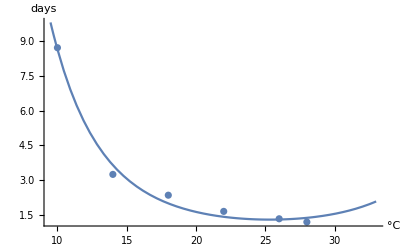

```mathematica
(*average egg stage duration*)
fitetol=gaussinvfit[ttimeseggtolarva]
plotstageduration[ttimeseggtolarva,fitetol]
```

{c1→5.13626,c2→25.3283,c3→11.0991}

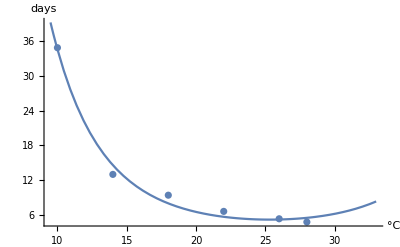

```mathematica
(*average larva stage duration*)
fitltop=gaussinvfit[ttimeslarvatopupa]
plotstageduration[ttimeslarvatopupa,fitltop]
```

{c1→4.58666,c2→25.7879,c3→11.1894}

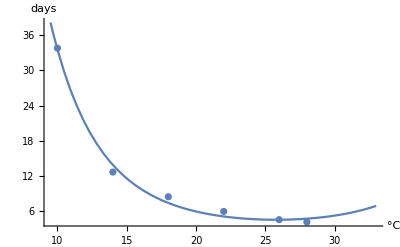

```mathematica
(*average pupa stage duration*)
fitptoa=gaussinvfit[ttimespupatoadult]
plotstageduration[ttimespupatoadult,fitptoa]
```

{c1→21.9962,c2→5.,c3→25.9266}

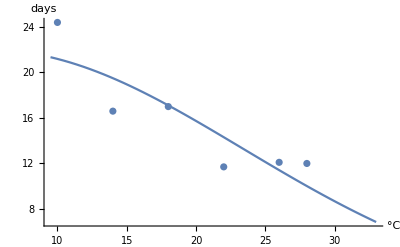

```mathematica
(*average adult life length*)
fitatom=FindFit[Transpose[{tochentemps,ttimesadulttomortality}],{gauss[c],c3>0,c2==5},{{c1,25},{c2,5},{c3,100}},c]
Show[{ListPlot[Transpose[{tochentemps,ttimesadulttomortality}]],Plot[gauss[c]/.fitatom,{c,9.5,33},PlotRange->Full]},AxesLabel->{"°C","days"},PlotRange->All]
```

```mathematica
plotmortalityrates[data_,fit_]:=Show[{ListPlot[Transpose[{tochentemps,data}]],Plot[gaussinv[c]/.fit,{c,9.5,30},PlotRange->Full]},AxesLabel->{"°C","1/day"},PlotRange->All];
```

{c1→0.0141035,c2→17.6847,c3→7.8393}

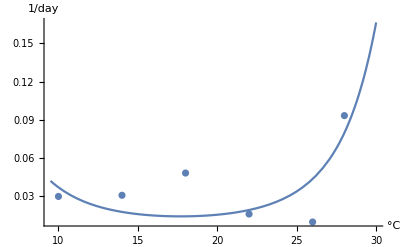

```mathematica
fitjmort=gaussinvfit[survivaldat]
plotmortalityrates[survivaldat,fitjmort]
```

{c1→1.635,c2→21.9048,c3→6.07961}

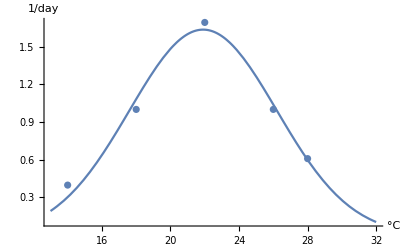

```mathematica
(*fecundity of females*)
fitfecundity=FindFit[fecunditydattemp,{gauss[c],c3>0},{{c1,10},{c2,30},{c3,10}},c]
Show[{ListPlot[fecunditydattemp],Plot[gauss[c]/.fitfecundity,{c,13,32},PlotRange->Full]},AxesLabel->{"°C","1/day"},PlotRange->All]
```